```mathematica
<<PlotLegends`
```

```mathematica
(* ЗАДАНИЕ 1 *)

plotParameters={
{Abs[x],{Yellow,Thick}},
{x^3,          {Blue,Dashed}},
{Sqrt[x],   {Black,Thin}}
};

xRange={-2,4};
yRange={-6,15};
functions=plotParameters[[All,1]];
colors=plotParameters[[All,2]];

graphs=Plot[functions,
			Evaluate[Join[{x}, xRange]],
			PlotRange->{xRange,yRange},
			PlotStyle->colors,
			Filling->{{2->{{3},Directive[{Lighter[Blue,0.7],Opacity[1]}]}},
					{3->{Axis,Directive[{Lighter[Red,0.3],Opacity[0]}]}}}
			
			(*PlotLabel->"Задание 1",
			PlotLegend->{functions⟦1⟧,functions⟦2⟧,functions⟦3⟧},
			Background->LightOrange,
			LegendPosition->{.5,-.9},
			LegendBackground->LightPurple,
			LegendSize->{0.5,0.5}*)
];


NINTPOINTS=3;
s=1/100;

integerPoints={};
For[i=1,i<=NINTPOINTS,i++,
integerPoints=Append[integerPoints, {x,y}/.NSolve[x==y,{x,y},Integers]/.y->i-2];
];

rectangles = {};
For[i=1,i<=NINTPOINTS,i++,
rectangles=Append[rectangles, Polygon[{{0+integerPoints⟦i⟧⟦1⟧⟦1⟧,s/1*Sqrt[3]+integerPoints⟦i⟧⟦1⟧⟦2⟧},{-s/2+integerPoints⟦i⟧⟦1⟧⟦1⟧,-s/2*Sqrt[3]+integerPoints⟦i⟧⟦1⟧⟦2⟧},{s/2+integerPoints⟦i⟧⟦1⟧⟦1⟧,-s/2*Sqrt[3]+integerPoints⟦i⟧⟦1⟧⟦2⟧}}]];
];
plottedTriangles=Graphics[rectangles];


Show[graphs,plottedTriangles,
			PlotLabel->"Задание 1",
			Background->Lighter[Orange,0.75]
			(*PlotLegend->{functions⟦1⟧,functions⟦2⟧,functions⟦3⟧},*)
			(*LegendPosition->{.5,-.9},
			LegendBackground->LightPurple,
			LegendSize->{0.5,0.5}*)
]

(*(x-1)^2/25+(y+2)^2/9<=1*)
(*Cleaning:*)
Remove["Global`*"]
```

-Graphics-

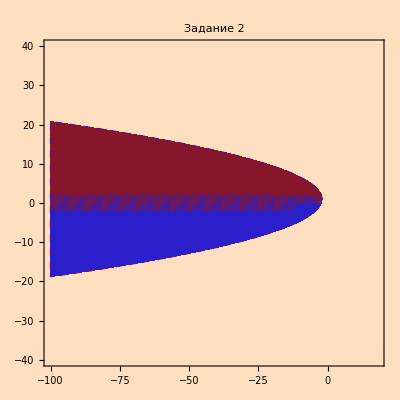

```mathematica
(* ЗАДАНИЕ 2 *)


f[x_,y_]:=y^2-2*y+4*x+9
xRange={-100,18};
yRange={-40,40};
graph=RegionPlot[f[x,y]<=0,
			Evaluate[Join[{x},xRange]],
			Evaluate[Join[{y},yRange]],
			PlotRange->{xRange,yRange},
			BoundaryStyle->{Darker[Red,0.5],Dashed, Thin},
			ColorFunction->"ThermometerColors",
			ColorFunctionScaling->False
(*{Directive[{Lighter[Blue,0.85],Opacity[0.8]}]}*)
			(*PlotLegend->{f[x,y]==0},*)
			FrameLabel->{"x","y"},
			RotateLabel->False
];

Show[graph,
	PlotLabel->"Задание 2",
	Background->Lighter[Orange,0.75],
	Axes->True
]

(*Cleaning:*)
Remove["Global`*"]
Clear[f]
```

```mathematica
(* ЗАДАНИЕ 3.1 *)


r[ϕ_]:=(10*Cos[ϕ])/(Sin[ϕ])^2
eps=0.1;
fRange={0+eps,π-eps};
rMax=Maximize[{r[ϕ],fRange⟦1⟧<=ϕ<=fRange⟦2⟧},ϕ]
graph=PolarPlot[r[ϕ],
				{ϕ,0+eps,π-eps},
				ColorFunction->Function[{x,y,ϕ,r},Hue[Abs[(√(x^2+y^2))/rMax⟦1⟧]]],
				ColorFunctionScaling->False(*True*)
				(*PlotLabels->r==r[ϕ]*)
];

Show[graph,
	(*PlotLabel->"Задание 3.1",*)
	Background->Lighter[Orange,0.7],
	Axes->True
]

(*Cleaning:    √(x^2+y^2)
ColorFunction->Function[{x,y},Hue[√(x^2+y^2)]],
r[ϕ_]:=16/(5-3*Cos[ϕ])*)

Remove["Global`*"]
Clear[r]
```

{998.327,{ϕ→0.1}}

-Graphics-

```mathematica
(* ЗАДАНИЕ 3.2 *)


f[x_,y_,z_]:=x^2/4+y^2/16+z^2/25
xRange={-3,3};
yRange={-5,5};
zRange={-6,6};
graph=ContourPlot3D[f[x,y,z]==1,
			Evaluate[Join[{x},xRange]],
			Evaluate[Join[{y},yRange]],
			Evaluate[Join[{z},zRange]],
			PlotRange->{xRange,yRange,zRange},
			ColorFunction->Function[{x,y,z},Hue[Abs[x]/(xRange⟦2⟧-xRange⟦1⟧)]],
			ColorFunctionScaling->False
];

Show[graph,
	PlotLabel->"Задание 3.2\n"f[x,y,z]==1,
	Background->Lighter[Orange,0.8],
	Axes->True,
	AxesLabel->{x,y,z}
]

(*Cleaning:*)
Remove["Global`*"]
Clear[f]
```

-Graphics3D-